# Final Machine Learning Project Course: Introduction to Mathematica 5 cr Student Name: Muhammad Ishfaq

## In this project, There are three Machine learning models have been developed and tested.

In this project BuiltIn dataset from Mathematica have been used. The project is divided into two section. Where two different aaproches of Machine learning have been used, 
In the First section Neural network have been used to recognize thousands of hand written digits. The Dataset is builtin but it can also be found online at “https://www.tensorflow.org/datasets/catalog/mnist”.
The objective of the first section is to use neural network  machine learning algorithms and predict the digits. In the end of the section,  some measures were  such as accuracy have been tested.  
In this section Unsupervised machine learning with Neural network has been used. AutoEncoder  has been used for this project, This is done only for reducing overload for loading many resources.

#### In the second section of this project UnSupervised machine learning modes have been used to make prediction and clustering for CIRAF dataset.

In the section Mathematica builtin dataset has been used to implement machine learning model. The main objective of  this section is to use  basic Machine learning algorithms in Mathematica to use Clustering algorithms. The dataset for this section is builtin but it can also be accessed at “Buitin and it can be accessed using ResourceData or ResourceObject”.   The implementation is done in the end.

Loading MINIST dataset from Mathematica and loading builtin training and testing data from this Dataset.

#### Loading MINIST Dataset

The MNIST Dataset is loaded and it is divided into training and testing data.  The selected TrainingData and TestData are already done by Mathematica.  Everything is located under the Resource data. In this section the length of data is tested as well.  For machine learning normally datasets are divided into two section to train and test data, in order to validate and check accuracy of predicted models and classified models.

```mathematica
resource = ResourceObject["MNIST"];
```

```mathematica
training = ResourceData[resource, "TrainingData"];
```

```mathematica
test = ResourceData[resource, "TestData"];
Length[training]
```

60000

```mathematica
Length[test]
```

10000

The training dataset is  used to see the hand written digits.  Total hand written digits are originally from 1 to 10. They are written in different format and have been classified into correct format. As the output has been shown in the output.

```mathematica
training[{1;;10}]
```

The similar way is done with RandomSample for training data. 10 Random sample are shown in output.  For optimization purposes only few random sample are selected. If the Number of selected random samples are even more the resutls will be the same, Hence, it will only make extra load into the Notebook.

```mathematica
RandomSample[training, 10]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→7,-Graphics-→1,-Graphics-→6,-Graphics-→8,-Graphics-→2,-Graphics-→1,-Graphics-→8,-Graphics-→0}

Here first element is selected and in the data it is shown

```mathematica
training[[1, 1]]
```

-Graphics-

```mathematica
training[[1, 2]]
```

0

Here data of images are flatten to make it as a list

```mathematica
Flatten[ImageData[training[[1, 1]]]];
```

Here  function is called

```mathematica
inputtraining[n_Integer]:=Flatten[ImageData[training[[n, 1]]]]
```

The same thing can be done with Testing data.

In order to find the index of each digit in the dataset, values are given with training and testing data. By doing so, we are able to find the index of each digit.

```mathematica
inputtest[n_Integer]:=Flatten[ImageData[test[[n, 1]]]]
```

```mathematica
valuetraining[n_Integer]:=training[[n, 2]]
valuettest[n_Integer]:= test[[n, 2]]
valuetraining[2]
```

0

```mathematica
valuettest[1]
```

0

#### Using Auto-encoder. The encoder is used to optimize the machine learning model in order to reduce the load on the notebook or on standalone machine. The same approach can be applied to Cloud Mathematica.

```mathematica
resource = ResourceObject["MNIST"];
trainingData = ResourceData[resource, "TrainingData"];
trainingSubset = Select[trainingData, Last[#]<=4&];
testData = ResourceData[resource, "TestData"];
testSubset = Select[testData, Last[#]<= 4&];
RandomChoice[trainingSubset, 8]
```

{-Graphics-→0,-Graphics-→3,-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→1,-Graphics-→1,-Graphics-→1}

In order to get mean image and subtract it from training data. It is removed to see the actual performance of training and testing data for Machine learning.

```mathematica
trainimage = Keys[trainingSubset];
meanImage = Image[Mean@Map[ImageData, trainimage]]
```

-Graphics-

A network is trained in order to get both reconstruction and the reconstruction error.  The NetGraph is used for neural layers.

```mathematica
net = NetGraph[{FlattenLayer[], 50, Ramp, 784, Tanh, ReshapeLayer[{1, 28, 28}], MeanSquaredLossLayer[]}, 
{1->2->3->4->5->6->NetPort["Output"],6-> NetPort[7, "Input"], 
NetPort["Input"]->NetPort[7, "Target"]},
"Input"->NetEncoder[{"Image", {28, 28},"Grayscale", "MeanImage"->meanImage}], "Output"->NetDecoder[{"Image", "Grayscale"}]
]
```

NetGraph[<>]

The network is trained in order to minimize the reconstruction errors.

```mathematica
train = If[$VersionNumber<11.3, NetTrain[net,<|"Input"->trainimage|>, "Loss"],
NetTrain[net, <|"Input"->trainimage|>, LossFunction->"Loss"]];
```

In order to obtain a subnetwork which performs which only reconstruction.

```mathematica
reconstruct = Take[train,{NetPort["Input"], NetPort["Output"]}]
```

NetGraph[<>]

The reconstruction of sample image is done here to train and test and validate the digit recognition.

```mathematica
ImageAdd[reconstruct[#], meanImage]&/@{-Graphics-, -Graphics-, -Graphics-,  -Graphics-,-Graphics- }
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

In order to get subnetwork which produces the code in a vector code. The code is given below.

```mathematica
encode = Take[train,{NetPort["Input"], 4}]
```

NetGraph[<>]

Here we compute the all image test and code is shown is here.  The image set is divided into test images to test images from subsets. It also get features

```mathematica
testimage = Keys[testSubset];
features = encode[testimage];
```

The vectors are coded into three vectors dimensions. And the visualization is done with the original classes which has not been yet seen by network.  Hence, the digits images are seen as cluster together.

```mathematica
corder = DimensionReduce[features, 3];
classes = Values[testSubset];
Table[Extract[corder, Position[classes,i]],{i, 0, 4}]
ListPointPlot3D[Table[Extract[corder, Position[classes,i]],{i, 0,4}], PlotLegends->PointLegend[96, Range[0,4]],BoxRatios->1, Axes->None, Boxed->True, PlotStyle->Map[ColorData[96], Range[1, 5]],AspectRatio->1]
```

-Graphics3D-

Here automatic clustering is performed which is directly on the code vectors and it has been show in the sample which is taken from each cluster. It shows the position of each hand written digits are displayed.

```mathematica
comps = ClusteringComponents[features, 5,1];
Map[Part[testimage, RandomSample[#, 10]]&,PositionIndex[comps] ]
```

<|1→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},3→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},4→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},5→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

The visualization is done in order to see hierarchical clustering of random attributes from every class in the network.

```mathematica
represent = Catenate@GroupBy[testSubset,Last->First,RandomSample[#, 6]&];
ClusteringTree[encode[represent]->Map[ImageCrop, represent]]
```

-Graphics-

## Classification for digits using classify to predict right classification of hand written digits.

The MNIST dataset is used in this section to classify hand written image digits to train and test a Convolutional network to make prediction the digits given in the dataset. To get data for training and validation data.

```mathematica
resourceclass = ResourceObject["MNIST"];
trainedData = ResourceData[resourceclass, "TrainingData"];
testingData = ResourceData[resourceclass, "TestData"];
```

```mathematica
RandomSample[trainingData, 10]
```

{-Graphics-→4,-Graphics-→6,-Graphics-→3,-Graphics-→4,-Graphics-→7,-Graphics-→1,-Graphics-→1,-Graphics-→8,-Graphics-→3,-Graphics-→5}

Here a Convolutional neural network is used in order to take 28 by 28 with grayscale image as input.

Here we can see how the classify function is learning about digit recognition.

```mathematica
lenet = NetChain[{ConvolutionLayer[20, 5], Ramp, PoolingLayer[2, 2], FlattenLayer[], 500, Ramp, 10, SoftmaxLayer[]}, 
"Output"->NetDecoder[{"Class", Range[0, 9]}],
"Input"->NetEncoder[{"Image", {28, 28}, "Grayscale"}]]
```

NetChain[<>]

The network is trained for 5 rounds for training on the data.  The minimum round are chosen to minimize load on the machine and also get resutls quicky with small rounds.

```mathematica
lenet = NetTrain[lenet, trainingData, ValidationSet->testData, MaxTrainingRounds->4];
```

The networks are trained and evaluate the network directly on the images which is randomly sampled from the validation dataset.

```mathematica
images = Keys@RandomSample[testData, 5];
Thread[images->lenet[images]]
```

{-Graphics-→1,-Graphics-→9,-Graphics-→2,-Graphics-→4,-Graphics-→2}

```mathematica
?*Layer
```

The builtin Layers are given in Mathematica. Layers are differentiable. It is a key property for computation. The Layers input and output are in an array and to use various layers , Net Encoders are used.

#### Calculating accuracy

```mathematica
N[Total[Table[KroneckerDelta[ClaasifierFunction[test[[i, 1]]],test[[i, 2]]], {i,1,10000}]]/ 10000]
```

With network, we may find it optimal and better way
Using existing networks within Mathematica.

```mathematica
network = NetModel["LeNet Trained on MNIST Data" ]
```

NetChain[<>]

#### Calculating accuracy with network. hidden layers are taken with this functions.

```mathematica
N[Total[Table[KroneckerDelta[network[test[[i, 1]]],test[[i, 2]]], {i,1,10000}]]/ 10000]
```

0.9848

```mathematica
Table[network[[i]], {i, 1, 11}]
```

{ConvolutionLayer[<>],ElementwiseLayer[<>],PoolingLayer[<>],ConvolutionLayer[<>],ElementwiseLayer[<>],PoolingLayer[<>],FlattenLayer[<>],LinearLayer[<>],ElementwiseLayer[<>],LinearLayer[<>],SoftmaxLayer[<>]}

```mathematica
Information[network, "SummaryGraphic"]
```

-Graphics-

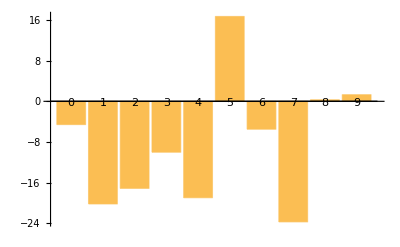

```mathematica
BarChart[Take[network, 10][-Graphics-], ChartLabels->Range[0, 9]]
```

The above BarChart shows the prediction of digit and its accuracy score. As we can see there were other two digits which were similar predict with lowest score 8 and 9 digits and rest of the digits have negative score.

#### Training Model

```mathematica
lenet = NetChain[{ConvolutionLayer[20, 5], Ramp, PoolingLayer[2, 2], ConvolutionLayer[50, 5],
Ramp, PoolingLayer[2, 2], FlattenLayer[], 
500, Ramp, 10, SoftmaxLayer[]
},
"Output" ->NetDecoder[{"Class", Range[0, 9]}],
"Input" ->NetEncoder[{"Image", {28, 28}, "Grayscale"}]
]
```

NetChain[<>]

```mathematica
NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

#### Changed neural network to see the better results.

```mathematica
network = NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
network[[10]]
```

LinearLayer[<>]

```mathematica
Information[network, "SummaryGraphic"]
```

-Graphics-

```mathematica
NetDrop[network, -3]
```

NetChain[<>]

```mathematica
LinearLayer[2, "Input" -> 500]
```

LinearLayer[<>]

```mathematica
NetChain[{NetDrop[network, -2],LinearLayer[2, "Input"->500],
 SoftmaxLayer["Input" -> 2]},
 "Output"->NetDecoder[{"Class", {"Normal", "mirrored"}}]]
```

NetChain[<>]

```mathematica
networkmirror = NetChain[{NetDrop[network, -2], 2, SoftmaxLayer[]}, "Output"->NetDecoder[{"Class", {"Normal", "mirrored"}}]]
```

NetChain[<>]

```mathematica
Information[networkmirror, "SummaryGraphic"]
```

-Graphics-

#### Other Machine Learning techniques to recognize images

In this section,  CIFAR -100 Dataset. The Dataset is developed at Canadian Institute of Advanced research.  The dataset consist of 50000 color images of 32 by 32 and classified in 100 classes.  This is a builtin Dataset which means it can be directly accessed from Mathematica builtin library.  In this section model is trained and find accuracy of classified images based on this dataset and also based on the implemented neural models. 
First dataset is loaded into Mathematica.

```mathematica
CirafData = ResourceData["CIFAR-100"]
```

```mathematica
CiraftrainingData = RandomSample[CirafData, 100];
```

```mathematica
trainingData=ResourceData[CirafData,"TrainingData"];
testData=ResourceData[CirafData,"TestData"];
```

```mathematica
RandomSample[CirafData, 50]
```

{-Graphics-→telephone,-Graphics-→wolf,-Graphics-→trout,-Graphics-→plain,-Graphics-→pine tree,-Graphics-→pear,-Graphics-→plate,-Graphics-→chair,-Graphics-→baby,-Graphics-→bus,-Graphics-→forest,-Graphics-→telephone,-Graphics-→beetle,-Graphics-→pine tree,-Graphics-→tractor,-Graphics-→palm tree,-Graphics-→snake,-Graphics-→flatfish,-Graphics-→orchid,-Graphics-→flatfish,-Graphics-→tiger,-Graphics-→trout,-Graphics-→mushroom,-Graphics-→seal,-Graphics-→rabbit,-Graphics-→tulip,-Graphics-→computer keyboard,-Graphics-→plain,-Graphics-→lion,-Graphics-→fox,-Graphics-→girl,-Graphics-→skyscraper,-Graphics-→palm tree,-Graphics-→dinosaur,-Graphics-→wolf,-Graphics-→dolphin,-Graphics-→tulip,-Graphics-→lawn-mower,-Graphics-→ray,-Graphics-→orange,-Graphics-→cloud,-Graphics-→tulip,-Graphics-→boy,-Graphics-→orange,-Graphics-→lawn-mower,-Graphics-→lizard,-Graphics-→bicycle,-Graphics-→possum,-Graphics-→orange,-Graphics-→can}

NetEncoder and NetDeconder  are used to handle the data from image to array and from array to image.

```mathematica
ecode = NetEncoder[{"Image", {32, 32}, "MeanImage"->0.5}]
```

NetEncoder[<>]

```mathematica
ecode[-Graphics-]//Dimensions
```

{3,32,32}

Find clusters of similar images using cluster method. However,  it returns the random images from the data it has been taken.

```mathematica
FindClusters[{CiraftrainingData }]
```

{{{-Graphics-→skyscraper,-Graphics-→caterpillar,-Graphics-→hamster,-Graphics-→cattle,-Graphics-→camel,-Graphics-→pine tree,-Graphics-→cockroach,-Graphics-→worm,-Graphics-→elephant,-Graphics-→kangaroo,-Graphics-→tiger,-Graphics-→whale,-Graphics-→bear,-Graphics-→plain,-Graphics-→dolphin,-Graphics-→oak tree,-Graphics-→woman,-Graphics-→rocket,-Graphics-→oak tree,-Graphics-→apple,-Graphics-→mushroom,-Graphics-→bus,-Graphics-→cockroach,-Graphics-→wolf,-Graphics-→skyscraper,-Graphics-→man,-Graphics-→otter,-Graphics-→aquarium fish,-Graphics-→dolphin,-Graphics-→porcupine,-Graphics-→beaver,-Graphics-→telephone,-Graphics-→pear,-Graphics-→kangaroo,-Graphics-→forest,-Graphics-→lamp,-Graphics-→tank,-Graphics-→kangaroo,-Graphics-→mountain,-Graphics-→computer keyboard,-Graphics-→hamster,-Graphics-→mushroom,-Graphics-→castle,-Graphics-→sunflower,-Graphics-→raccoon,-Graphics-→wolf,-Graphics-→bowl,-Graphics-→boy,-Graphics-→lamp,-Graphics-→skunk,-Graphics-→bear,-Graphics-→rabbit,-Graphics-→squirrel,-Graphics-→plate,-Graphics-→lawn-mower,-Graphics-→castle,-Graphics-→motorcycle,-Graphics-→wolf,-Graphics-→worm,-Graphics-→maple tree,-Graphics-→flatfish,-Graphics-→tiger,-Graphics-→trout,-Graphics-→mushroom,-Graphics-→tulip,-Graphics-→man,-Graphics-→can,-Graphics-→mouse,-Graphics-→poppy,-Graphics-→cup,-Graphics-→cup,-Graphics-→oak tree,-Graphics-→beetle,-Graphics-→woman,-Graphics-→chair,-Graphics-→train,-Graphics-→maple tree,-Graphics-→mouse,-Graphics-→crab,-Graphics-→baby,-Graphics-→beaver,-Graphics-→bear,-Graphics-→pickup truck,-Graphics-→streetcar,-Graphics-→camel,-Graphics-→woman,-Graphics-→pine tree,-Graphics-→cockroach,-Graphics-→skunk,-Graphics-→bicycle,-Graphics-→television,-Graphics-→trout,-Graphics-→butterfly,-Graphics-→house,-Graphics-→bus,-Graphics-→camel,-Graphics-→cloud,-Graphics-→dinosaur,-Graphics-→skyscraper,-Graphics-→cup}}}

In order to make clusters of similar images, feature space builtin function is used to get required results. By giving different types of images as an input will provide the required clusters. The number of clusters are made on the basis of given input images.

```mathematica
FeatureSpacePlot[{-Graphics-,-Graphics-, -Graphics-, -Graphics-, -Graphics-,  -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-,  -Graphics-, -Graphics-,-Graphics-,  -Graphics-,-Graphics-,-Graphics- }]
```

-Graphics-

The result of FeatureSpace plot is given above as it is shown the images are placed far from each others which seems in a wrong order. Some other clustering technique is used to make right clusters out of these images.

```mathematica
Dendrogram[{-Graphics-,-Graphics-, -Graphics-, -Graphics-, -Graphics-,  -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-,  -Graphics-, -Graphics-,-Graphics-,  -Graphics-,-Graphics-,-Graphics- }]
```

-Graphics-

The Dendrogram Clustering Machine learning technique provides better results than the previous obtained resutls from FeatureSpace Machine Learning technique has provided.  
The last clustering technique for image is used clustering tree.

```mathematica
ClusteringTree[{-Graphics-,-Graphics-, -Graphics-, -Graphics-, -Graphics-,  -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-,  -Graphics-, -Graphics-,-Graphics-,  -Graphics-,-Graphics-,-Graphics- }]
```

-Graphics-

With Clustering tree, The result is much better, as it is shown in the tree Clustering tree finds the most relevant images at least in the same tree node from tree parent to its child or root node which is similair to the parent node image type.

#### Object Classification for CIRAF-10 data, in this section classification unsupervised Machine Learning approach is used to classify images. In the end the validation is done in order to see how the classified images are made using neural networks.

```mathematica
imageObject = ResourceObject["CIFAR-10"];
traningdata = ResourceData[imageObject, "TrainingData"];
ciraftest = ResourceObject["CIFAR-10", "TestData"];
RandomSample[traningdata , 5]
```

{-Graphics-→bird,-Graphics-→dog,-Graphics-→ship,-Graphics-→dog,-Graphics-→automobile}

Here unique classes are presented with union function.

```mathematica
class = Union@Values[traningdata ]
```

{airplane,automobile,bird,cat,deer,dog,frog,horse,ship,truck}

Here Convolutional net is used which predicts the class with given image.

```mathematica
lenet = NetChain[{ConvolutionLayer[20, 5], Ramp, PoolingLayer[2, 2], ConvolutionLayer[50, 5], Ramp, PoolingLayer[2, 2], FlattenLayer[], 500, Ramp, 10, SoftmaxLayer[] },
"Output"->NetDecoder[{"Class", class}],
"Input"->NetEncoder[{"Image", {28, 28}}]]
```

NetChain[<>]

Training the net on Train data.  This is done due to constructing Neural Network.

```mathematica
traineeData = NetTrain[lenet, traningdata, MaxTrainingRounds->4]
```

NetChain[<>]

After training the prediction is made for most likely classes for given a set of an images.

```mathematica
traineeData [{-Graphics-, -Graphics-, -Graphics-,-Graphics- }]
```

{dog,cat,deer,truck}

Here, some of samples of image probabilities are given which are label assignments.

```mathematica
traineeData[-Graphics-, {"TopProbabilities", 5}]
```

{ship→0.0557673,dog→0.153146,cat→0.163743,horse→0.271927,truck→0.297522}

Above given 5 probabilities  are measured against the given image in the function.

From the random sample, the images are selected that gives the highest and lowest score prediction.  High Entropy means the net is most likely to not able to predict correct class and low score means the net is able predict the image in the correct class.

```mathematica
cfm = ClassifierMeasurementsObject[lenet, traineeData]
```

MachineLearning`file143ClassifierPredictor`PackagePrivate`routerObject[NetChain[<>],NetChain[<>],Report,<|ClassPriors→Automatic,ComputeUncertainty→False,IndeterminateThreshold→Automatic,MissingValueSynthesis→Automatic,PerformanceGoal→Automatic,RandomSeeding→1234,TargetDevice→CPU,TieBreakerFunction→RandomChoice,UtilityFunction→Automatic,Weights→Automatic,Separator→Null|>]

```mathematica
cfm["Accuracy"]
```

MachineLearning`file143ClassifierPredictor`PackagePrivate`routerObject[NetChain[<>],NetChain[<>],Accuracy,<|ClassPriors→Automatic,ComputeUncertainty→False,IndeterminateThreshold→Automatic,MissingValueSynthesis→Automatic,PerformanceGoal→Automatic,RandomSeeding→1234,TargetDevice→CPU,TieBreakerFunction→RandomChoice,UtilityFunction→Automatic,Weights→Automatic,Separator→Null|>]

confusion Matrix is used to make network prediction on the validation sets.

```mathematica
cfm["ConfusionMatrixPlot"]
```

MachineLearning`file143ClassifierPredictor`PackagePrivate`routerObject[NetChain[<>],NetChain[<>],ConfusionMatrixPlot,<|ClassPriors→Automatic,ComputeUncertainty→False,IndeterminateThreshold→Automatic,MissingValueSynthesis→Automatic,PerformanceGoal→Automatic,RandomSeeding→1234,TargetDevice→CPU,TieBreakerFunction→RandomChoice,UtilityFunction→Automatic,Weights→Automatic,Separator→Null|>]

#### Classification of MNISTFashion Dataset.

Here classification for Fashion Dataset is used. In the first phase data is exracted and divided into training and testing data and then further data analysis is done and in the end confusion matrix is used to see the correctness of machine learning models. 
The objective of this section is to use “lenet” train model and make classification for 10 given categories.

```mathematica
FashionData = ResourceData["FashionMNIST", "TrainingData"];
```

```mathematica
fashionTest = ResourceData["FashionMNIST", "TestData"];
```

The data is labled as it is shown in the above output. This is  similar like a training or labelling datasets and later on the  labled class is used to train lenet with this settings.

```mathematica
fashionClass = {0->"T-shirt/top", 1->"Trouser", 2->"Pullover", 3->"Dress", 4->"Coat", 5->"Sandal", 6->"Shirt", 7->"Sneaker", 8->"Bag", 9->"Ankle boot"};
```

```mathematica
GroupBy[FashionData, Last->First, RandomChoice]//KeySort
```

<|0→-Graphics-,1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-,6→-Graphics-,7→-Graphics-,8→-Graphics-,9→-Graphics-|>

Model is trained on small data to see classification of image and set data as validation set.

```mathematica
fnet = NetTrain[NetModel["LeNet"],FashionData, ValidationSet->Scaled[.1]]
```

NetChain[<>]

Here, test dataset is sued to test the accuracy of a classifier.

```mathematica
NetMeasurements[fnet, fashionTest, "Accuracy"]
```

0.9094

Obtained accuracy for this classifier is 0.9094 which is quite good so we could say that this classifier works better in this approach. 
The next step is to make confusion matrix to see the classifier accuracy in visulization.

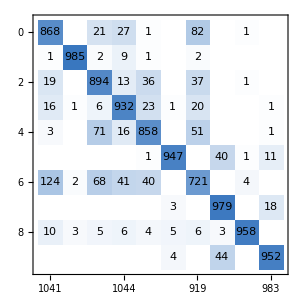
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[fnet, fashionTest, "ConfusionMatrixPlot"]
```

The above confusion matrix gives actual class and predicted class. The overall results from classifier are quite good, as it is shown in dark blue color the balancing accuracy. 
The plot is drawn in order to see the relationship between true positive rate and false positive rate as in a binary classifier.  This is shown by the average vitalization receiver operating characteristic(ROC) curve for every class.

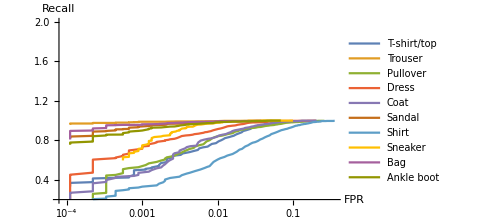

```mathematica
ListLinePlot[Values[Transpose/@NetMeasurements[fnet, fashionTest, "ROCCurve"]],PlotLegends->Values[fashionClass], ScalingFunctions->{"Log", None}, ImageSize->Medium, PlotRange->{All, {0.2,2}}, AxesLabel->{"FPR","Recall"}]
```

In the next phase, the average ROC is computed with all classes given in the dataset.

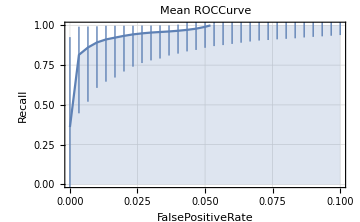

```mathematica
rclist = Interpolation@*Values@*(GroupBy[#1, First, Mean]&)@*Transpose/@Values[NetMeasurements[fnet, fashionTest,"ROCCurve"]];
ListLinePlot[Table[{i,With[{a=Mean[#]},Around[a,{a-Min[#],Max[#]-a}]]&@Quiet[Through[rclist[i]]]},{i,0.0,.1,.1/30}], Sequence[PlotRange->{{1/10^4, All}, {0,1}}, PlotTheme->"Detailed", PlotLabel->"Mean ROCCurve", FrameLabel->{"FalsePositiveRate","Recall"}, Filling->Axis, ImageSize->Medium]]
```

The recall false postive rate are displayed in the above graph. As we can see the better result with visulization The recall is from 0.4 to 0.98 approximately.

With the help of featurespace3D 3D visulization has been shown for dataset content.

```mathematica
FeatureSpacePlot3D[Keys[RandomSample[fashionTest,1000]],FeatureExtractor->NetDrop[fnet,-1],ImageSize->Medium]
```

-Graphics3D-

In the above 3D featureSpace various clusters have been made based on the nearest classification label.  Shoes are formed into one cluster, hand bags are in different cluster trouser, jeans are in one cluster shirts, t-shirts and other similair ladies and gents jackets are placed into one cluster. Therefore, the result from MNIST and classifiers have good classification accuracy.

In this project is has been seen when using machine learning for digit recognition. It has the limitations the Mathematica took too long to compute  all the hidden layer calculation to display all the data as output. The system itself has great scalability but standalone machine have some limitations. And, due to  lack of compute power on standalone machine it slow the entire process. However, this can be further scalable when using parallel and Distributed programming model in Mathematica.   On the other hand, it can also be achieved with cloud resources.  
It has been seen that how Mathematica is powerful than other computational tools for scientific data analysis and Machine learning.  The  Mathematica has great built in functions for Machine learning which makes even programmer  and scientist life easy. In this project further scientific data would be analysed but due to short time and limited resources  it was not possible. 
The chosen project deals with Machine learning using Neural networks. This project deals with machine learning and according to the machine learning models no scientific data analysis or Data preprocessing was not required due to usage of builtin datasets winthin Mathematica.  However, the project has potential as it has Machine learning project which have been divided into three sections.  Due to the limitations of time and resources further process was not possible to be done.